## Function that solves difference equation for equal likelihood Bernoulli trails

```mathematica
RuinFunction[pO_Integer,nO_Integer]:=Module[{function,helperfunction,rules,vereisten,i,j},function=RSolveValue[{a[k]==0.5* a[k+pO]+(1-0.5) a[k-nO]},a[k],k];
helperfunction=RSolveValue[{a[k]==0.5* a[k+pO]+(1-0.5) a[k-nO]},a[1],k];
loop=Length[function];
rules=List[];
For[i=1,i≤loop,i++,
If[Length[helperfunction[[i]]]>1,If[Norm[helperfunction[[i,1]]]<1,AppendTo[rules,Last[function[[i]]]->Last[function[[i]]]],AppendTo[rules,Last[function[[i]]]->0]],AppendTo[rules,function[[i]]->0]];
];
function=function/.rules;
vereisten=List[];
AppendTo[vereisten,Evaluate[function/.{k->0}]==1];
For[j=1,j<nO,j++,
AppendTo[vereisten,Evaluate[function/.{k->j-nO}]==1];
];
function/.First[Solve[vereisten]]]
```

## Generates data set for different starting allowances.

```mathematica
expectedValueList=Table[i,{i,0,50}];
SDList=Table[i,{i,0,100}];
outcomesoverEX1bet=List[];
StartAllowance=Prepend[Table[5*i,{i,1,20}],1];
For[indexExpect=1,indexExpect<=Length[expectedValueList],indexExpect++,(*Generates the different bernouilliu bets based on the expecetd value and standard deviation. These are then used to calculate the hitting probability*)
EX=expectedValueList[[indexExpect]];
outcomesoverSD=List[];
For[indexSD=1,indexSD≤Length[SDList],indexSD++,
SD=SDList[[indexSD]];
pO=EX+SD;(*positive outcome*)
nO=Abs[EX-SD]; (*magnitude negative outcome*)

If[EX==0&&SD ≠0,AppendTo[outcomesoverSD,{SD,EX,Table[1,{k,StartAllowance}]}],If[EX-SD<0,
z=(RuinFunction[pO,nO]);
outcome=Table[{z,k},{k,StartAllowance}];
AppendTo[outcomesoverSD,{SD,EX,Re[outcome[[All,1]]]}]
,AppendTo[outcomesoverSD,{SD,EX,Table[0,{k,StartAllowance}]}]] (*verifies the different cases. If E[x]=0 and SD ≠ 0 hitting the boundary is guaranteed in the time limit t-> Infty, Else you have a normal gamble with a positive and negative outcomes for which we have to calculate the hitting probability, or you have two positive outcomes im which case you can not hit the boundary.*)
]
];
outcomesoverEX1bet=Join[outcomesoverEX1bet,outcomesoverSD]
]
outcomesAllKapitalJump5and1=outcomesoverEX1bet;
```

General::munfl: (-0.716189-0.520342 ⅈ)^25 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-0.716189+0.520342 ⅈ)^25 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-0.716189-0.520342 ⅈ)^50 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
RuinFunction[3,2]
```

0.0664007 (-0.660993)^k+0.933599 0.848375^k

```mathematica
outcomesAllKapitalJump5and1="data";(*Preran Data, is the same as executing above functions*)
```

```mathematica
Prepend[Table[5*i,{i,1,20}],1]
```

{1,5,10,15,20,25,30,35,40,45,50,55,60,65,70,75,80,85,90,95,100}

## allowance =1

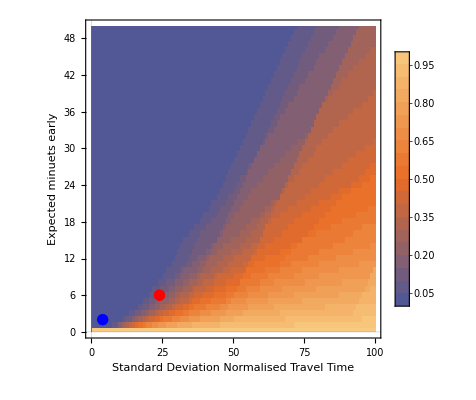

```mathematica
contourList=Table[0.05i,{i,0,20}];
allowance=19;
region90=Show[ListContourPlot[Transpose[Join[Transpose[outcomesAllKapitalJump5and1[[All,1;;2]]],{outcomesAllKapitalJump5and1[[All,3]][[All,allowance (*Check list (StartAllowance) x5 for true allowance and allowance=1 in beginning of list *)]]}]],PlotRange->{{0,100},{0,50},All},PlotLegends->Automatic,InterpolationOrder->0,Contours->contourList,FrameLabel->{{"Expected minuets early"},{"Standard Deviation Normalised Travel Time"}},PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},LabelStyle->Directive[FontFamily->"Times",Black,FontSize->16]],ListPlot[{{{24,6}},{{4,2}}},PlotStyle->{{PointSize[0.02],Red},{PointSize[0.02],Blue}}](*Reference Gambles in text*)]
```

```mathematica
Export["region90.pdf",region90]
```

region90.pdf

```mathematica
allowance =90
```

90

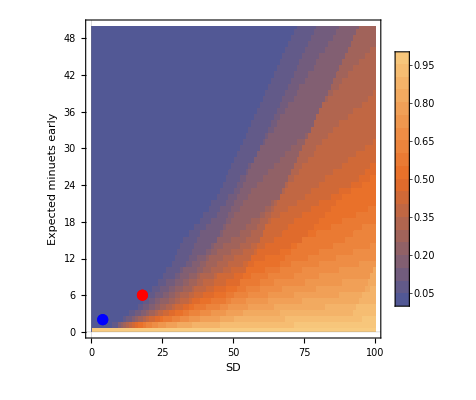

```mathematica
contourList=Table[0.05i,{i,0,20}];
allowance=19;
Show[ListContourPlot[Transpose[Join[Transpose[outcomesAllKapitalJump5and1[[All,1;;2]]],{outcomesAllKapitalJump5and1[[All,3]][[All,allowance (*Check list (StartAllowance) x5 for true allowance and allowance=1 in beginning of list *)]]}]],PlotRange->{{0,100},{0,50},All},PlotLegends->Automatic,InterpolationOrder->0,Contours->contourList,FrameLabel->{{"Expected minuets early"},{"SD"}},PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},LabelStyle->Directive[FontFamily->"Times",Black,FontSize->12]],ListPlot[{{{18,6}},{{4,2}}},PlotStyle->{{PointSize[0.02],Red},{PointSize[0.02],Blue}}](*Reference points first their Standard deviation then their expected value*)]
```